```mathematica
m1=67;
m2=2;
k1=34.5;
k2=34.5;
sol=NDSolve[{
m1*x1''[t]==-k1*x1[t]+k2(x2[t]-x1[t]),
m2*x2''[t]==-k2*(x2[t]-x1[t]),
x1[0]==10,
x1'[0]==2,
x2[0]==2,
x2'[0]==10},
{x1,x2},
{t,0,25}]
```

{{x1→InterpolatingFunction[{{0., 25.}}, <>],x2→InterpolatingFunction[{{0., 25.}}, <>]}}

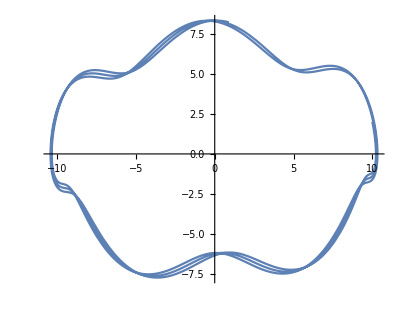

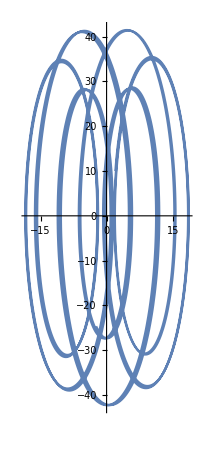

```mathematica
ParametricPlot[{x1[t],x1'[t]}/.sol,{t,0,25}]
ParametricPlot[{x2[t],x2'[t]}/.sol,{t,0,25}]
```